```mathematica
(* Copyright 2015 Thomas Trogdon & Deniz Bilman *)
(* This software is distributed under the terms of the GNU General Public License *)
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
AppendTo[$Path,"~/RHPackage"];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`Toda`;
```

## Initial data choices

```mathematica
A[n_]:=Product[2a[k],{k,n,500}];
B[n_]:=-Sum[b[k],{k,n+1,500}];
```

### Quad solition w/dispersion

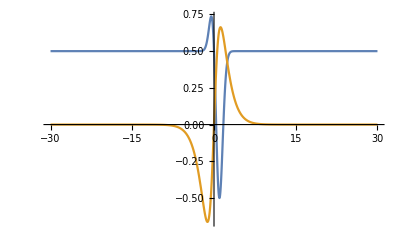

```mathematica
a[n_]:=1/2 - 1.n Exp[-n^2+n]//N;
b[n_]:=n Sech[n]//N;
Plot[{a[n], b[n]},{n,-30,30}]
ll=100;
```

### Double Soliton w/dispersion

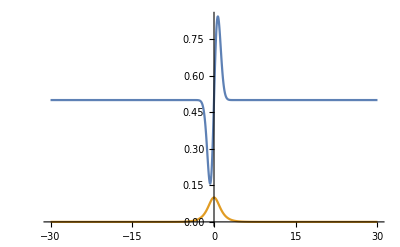

```mathematica
a[n_]:=1/2 +.8 n Exp[-n^2]//N;
b[n_]:=.1Sech[n]//N;
Plot[{a[n], b[n]},{n,-30,30}]
```

### Non-solitonic

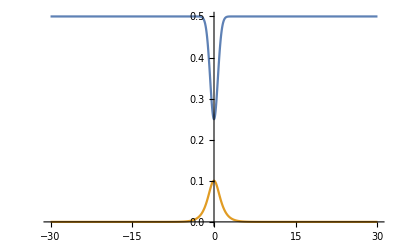

```mathematica
a[n_]:=1/2 -1/4 Exp[-n^2]//N;
b[n_]:=.1Sech[n]//N;
Plot[{a[n], b[n]},{n,-30,30}]
```

### Tiny soliton

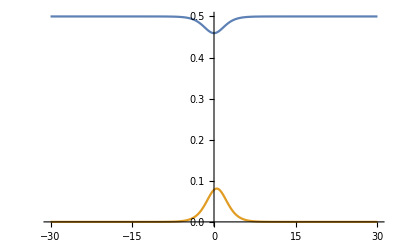

```mathematica
(*Flipped Soliton (no eigenvalues) data *)
aa[n_]:=1+Exp[-2(0.4)n];
a[n_]:=1.0 -(1/2 Sqrt[aa[n-1]aa[n+1]]/aa[n]);
zz=Exp[-(0.4)];
(*b[n_]:= 0;*)
b[n_]:=.9999 1/2(zz-zz^(-1))( (aa[n]-1)/aa[n] - (aa[n-1]-1)/aa[n-1])+.0000Exp[-n^2];
Plot[{a[n], b[n]},{n,-30,30}]
```

### Pure Soliton

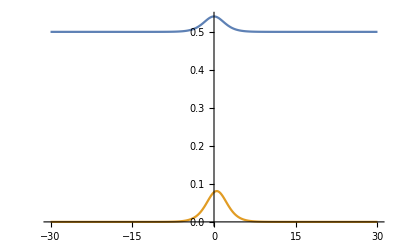

```mathematica
(*Soliton data *)
aa[n_]:=1+Exp[-2(0.4)n];
a[n_]:=1/2 Sqrt[aa[n-1]aa[n+1]]/aa[n];
zz=Exp[-(0.4)];
b[n_]:=1/2(zz-zz^(-1))( (aa[n]-1)/aa[n] - (aa[n-1]-1)/aa[n-1]);
Plot[{a[n], b[n]},{n,-30,30}]
```

## Setup Reflection Coefficients

```mathematica
(*scattering data for n ≥0*)
(*need to make this all more automatic*)
H1=ScatteringMatrixFiniteTodaC[a,b,ll];
aa1//Clear;bb1//Clear;
aa1[k_]:=aa1[k]=H1[k][[2,2]];
bb1[k_]:=bb1[k]=H1[k][[1,2]];
ρ1[k_]:=bb1[k]/aa1[k];
ρ1[1.]:=-1;
ρ1[-1.]:=-1;
ma1=LocatePolesToda[a,b,200]
mc1 =ResiduesToda[a,b,ma1,200]
(*scattering data for n < 0*)
(*
We only solve Toda for n ≥0.  It follows that if (a_n,b_n) solves Toda then (a_{-n},-b_{-n + 1}) also solves Toda.  So, if we solve Toda with initial data (a_{-n},-b_{-n+1}) to find (A_n, B_n) for only n > 0 then we can find (a_n,b_n) for n < 0  by the relation
(a_n,b_n) = (A_{-n}, - B_{-n+1}).
*)
H2=ScatteringMatrixFiniteTodaC[a[-#]&,-b[-#+1]&,ll];
aa2//Clear;bb2//Clear;
aa2[k_]:=aa2[k]=H2[k][[2,2]];
bb2[k_]:=bb2[k]=H2[k][[1,2]];
ρ2[k_]:=bb2[k]/aa2[k];
ρ2[1.]:=-1;
ρ2[-1.]:=-1;
ma2=LocatePolesToda[a[-#]&,-b[-#+1]&,200]
mc2=ResiduesToda[a[-#]&,-b[-#+1]&,ma2,200]

(*strip of analyticity guess*)
min = Min[.3,Join[Abs[ma1-1],Abs[ma1+1],Abs[ma2+1],Abs[ma2-1]]//Min];
(*setup scattering data*)
SetScatteringData[{ρ1,ma1,mc1},{ρ2,ma2,mc2}];
(*various parameters --- third: truncation tolerance, fourth: smallN, fifth: largeN*)
m=10;
SetParams[min/1.1,min/1.1,(10)^(-12),m,2m];
```

{-0.418827+0. ⅈ,0.488476,-0.815262+0. ⅈ,0.864527}

{0.00128482,4.40051,0.0000295525,0.904587}

{0.418827,-0.488476+0. ⅈ,0.815262,-0.864527+0. ⅈ}

{189.085,0.0371947,2.51586,0.0000530199}

## Quad soliton computations

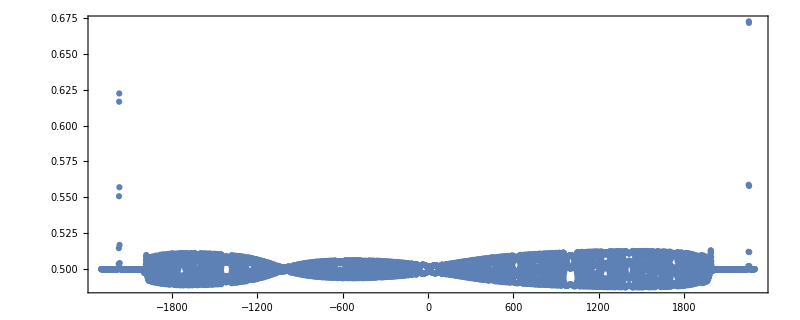

```mathematica
data1=Monitor[Table[{n,TodaabAuto[n,2000][[1]]//Re},{n,-2300,2300}],{n,contours}];
ListPlot[data1,Axes->False,Frame->True,AspectRatio->.4,ImageSize->800,FrameStyle->20,PlotRange->All]
```

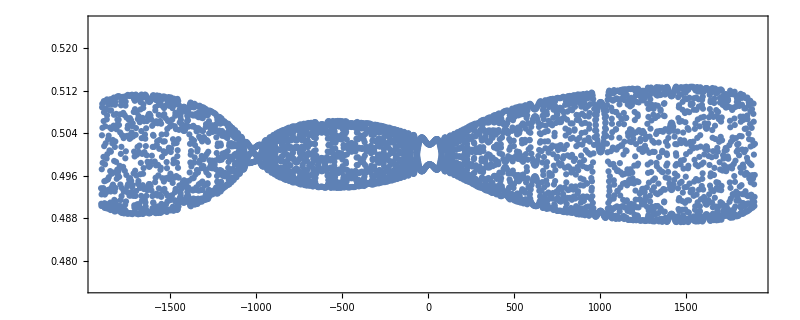

```mathematica
data1=Monitor[Table[{n,TodaabAuto[n,2000][[1]]//Re},{n,-1900,1900}],{n,contours}];
pl1=ListPlot[data1,Axes->False,Frame->True,AspectRatio->.4,ImageSize->800,FrameStyle->20,PlotRange->{{-1900,1900},{-.1,.1}/4+.5}]
```